```mathematica
ClearAll["Global`*"]
```

```mathematica
resultsPath="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/double-beta-pairing-strength/results/";
```

### Experimental data

```mathematica
ydataP={0.36,0.34,0.18,0.38,0.20,0.27,0.27,0.24};
ydataN={0.38,0.36,0.433,0.36,0.245,0.22,0.24,0.26};
xdata={76,82,96,100,116,128,130,150};
```

### Plot style

```mathematica
mystyle = {Frame -> True, Axes -> False,
    FrameLabel -> {"A", "G"}, FrameStyle -> Directive[Black, Thick], 
    LabelStyle -> {17, Bold, Black, FontFamily -> "Times"}, AspectRatio -> 0.8, 
    PlotMarkers -> {Red}};
```

### Model

```mathematica
(*the pairing strength for protons*)
gp[a_,b_,x_]:=b+a*1/x;
(*the pairing strength for protons*)
gn[c_,d_,x_]:=d+c*1/x;
```

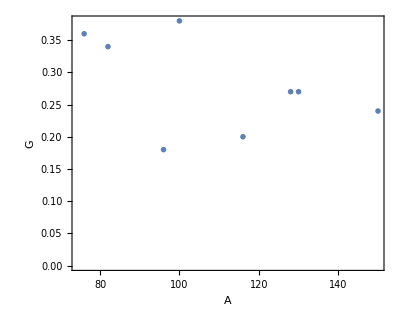

-Graphics-

```mathematica
expdataP=Table[{xdata[[i]],ydataP[[i]]},{i,1,Length[xdata]}];
expdataN=Table[{xdata[[i]],ydataP[[i]]},{i,1,Length[xdata]}];
figP=ListPlot[expdataP,Evaluate[mystyle]];
figN=ListPlot[expdataN,Evaluate[mystyle]];
Show[figP]
Show[figN]
```